```mathematica
Id=IdentityMatrix[3];sz={{1,0,0},{0,0,0},{0,0,-1}};sx=1/Sqrt[2]*{{0,1,0},{1,0,1},{0,1,0}};sy=1/Sqrt[2]*{{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Sz=KroneckerProduct[sz,Id];
Sx=KroneckerProduct[sx,Id];
Sy=KroneckerProduct[sy,Id];
szsquare=sz.sz;
Szsquare=KroneckerProduct[szsquare,Id];
izsquare=sz.sz;
Izsquare=KroneckerProduct[Id,izsquare];
Iz=KroneckerProduct[Id,sz];
Ix=KroneckerProduct[Id,sx];
Iy=KroneckerProduct[Id,sy];
He=De*Szsquare+gammae*(Bz*Cos[psi]*Sz+Bz*Sin[psi]*Cos[theta]*Sx+Bz*Sin[psi]*Sin[theta]*Sy)+Q*Izsquare+Cp*Sz.Iz+Cv*(Sx.Ix+Sy.Iy)+gamman*Bz*Iz+Subscript[E, es]*(Sx.Sx-Sy.Sy);psi=0;(*spherical coordinates*)
(*Eigenvalues[He];*)
Subscript[E, es]=0;He
```

{{Cp+De+Bz gammae+Bz gamman+Q,0,0,0,0,0,0,0,0},{0,De+Bz gammae,0,Cv,0,0,0,0,0},{0,0,-Cp+De+Bz gammae-Bz gamman+Q,0,Cv,0,0,0,0},{0,Cv,0,Bz gamman+Q,0,0,0,0,0},{0,0,Cv,0,0,0,Cv,0,0},{0,0,0,0,0,-Bz gamman+Q,0,Cv,0},{0,0,0,0,Cv,0,-Cp+De-Bz gammae+Bz gamman+Q,0,0},{0,0,0,0,0,Cv,0,De-Bz gammae,0},{0,0,0,0,0,0,0,0,Cp+De-Bz gammae-Bz gamman+Q}}

```mathematica
NewHe={{Bz gamman+Q,0,0,0,0,0},{0,0,0,Cv,0,0},{0,0,-Bz gamman+Q,0,Cv,0},{0,Cv,0,-Cp+De-Bz gammae+Bz gamman+Q,0,0},{0,0,Cv,0,De-Bz gammae,0},{0,0,0,0,0,Cp+De-Bz gammae-Bz gamman+Q}};(*gamman=0;*)Eigenvalues[NewHe]
Eigenvectors[NewHe]
```

{Cp+De-Bz gammae-Bz gamman+Q,Bz gamman+Q,1/2 (-Cp+De-Bz gammae+Bz gamman-√(4 Cv^2+(Cp-De+Bz gammae-Bz gamman-Q)^2)+Q),1/2 (-Cp+De-Bz gammae+Bz gamman+√(4 Cv^2+(Cp-De+Bz gammae-Bz gamman-Q)^2)+Q),1/2 (De-Bz gammae-Bz gamman+Q-√((-De+Bz gammae+Bz gamman-Q)^2-4 (-Cv^2-Bz De gamman+Bz^2 gammae gamman+De Q-Bz gammae Q))),1/2 (De-Bz gammae-Bz gamman+Q+√((-De+Bz gammae+Bz gamman-Q)^2-4 (-Cv^2-Bz De gamman+Bz^2 gammae gamman+De Q-Bz gammae Q)))}

{{0,0,0,0,0,1},{1,0,0,0,0,0},{0,-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q+√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2)),0,1,0,0},{0,-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q-√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2)),0,1,0,0},{0,0,-(De-Bz gammae+Bz gamman-Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv),0,1,0},{0,0,-(De-Bz gammae+Bz gamman-Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv),0,1,0}}

```mathematica
Simplify[-(De-Bz gammae+Bz gamman-Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv)*-(De-Bz gammae+Bz gamman-Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv)]
```

-1

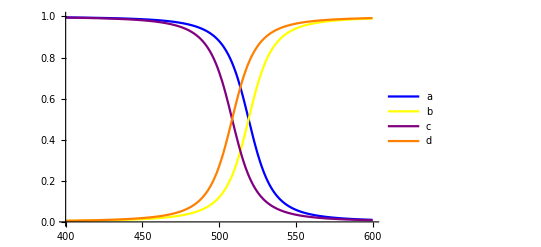

```mathematica
Q=-4.945;gammae=2.802;Cp=-40;Cv=-23;De=1420;gamman=-0.000308;
g1=Plot[(-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q+√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2)))^2/((-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q+√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2)))^2+1),{Bz,400,600},PlotStyle->Blue,PlotLegends->{"a"}];
g2=Plot[(-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q-√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2)))^2/((-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q-√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2)))^2+1),{Bz,400,600},PlotStyle->Yellow,PlotLegends->{"b"}];
g3=Plot[(-(De-Bz gammae+Bz gamman-Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv))^2/((-(De-Bz gammae+Bz gamman-Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv))^2+1),{Bz,400,600},PlotStyle->Purple,PlotLegends->{"c"}];
g4=Plot[(-(De-Bz gammae+Bz gamman-Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv))^2/((-(De-Bz gammae+Bz gamman-Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv))^2+1),{Bz,400,600},PlotStyle->Orange,PlotLegends->{"d"}];
g5=Plot[(-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q+√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2)))*(-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q-√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2))),{Bz,400,600},PlotStyle->Black,PlotLegends->{"3*4"}];
g6=Plot[(-(De-Bz gammae+Bz gamman-Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv))*(-(De-Bz gammae+Bz gamman-Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv)),{Bz,400,600},PlotStyle->Red,PlotLegends->{"5*6"}];
g7=Plot[-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q+√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2))*(-(De-Bz gammae+Bz gamman-Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv))*-1/(2 Cv)(-Cp+De-Bz gammae+Bz gamman+Q-√(Cp^2+4 Cv^2-2 Cp De+De^2+2 Bz Cp gammae-2 Bz De gammae+Bz^2 gammae^2-2 Bz Cp gamman+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 Cp Q+2 De Q-2 Bz gammae Q+2 Bz gamman Q+Q^2))*(-(De-Bz gammae+Bz gamman-Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2+2 Bz De gamman-2 Bz^2 gammae gamman+Bz^2 gamman^2-2 De Q+2 Bz gammae Q-2 Bz gamman Q+Q^2))/(2 Cv)),{Bz,400,600},PlotStyle->Gray,PlotLegends->{"3*4*5*6"}];(*Show[g5,PlotRange->{{400,600},{-20,20}},AxesLabel->{B[G],P }]*)
Show[g1,g2,g3,g4,PlotRange->{{400,600},{0,1}},AxesLabel->{B[G]}]
```

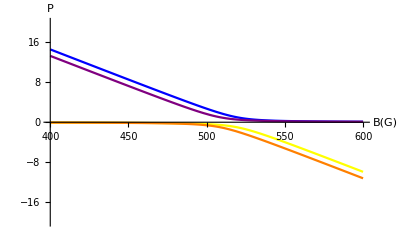

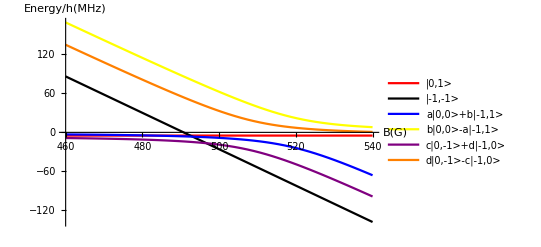

```mathematica
Q=-4.945;gammae=2.802;Cp=-40;Cv=-23;De=1420;
F1[Bz_]:=Q;
F2[Bz_]:=Cp+De-Bz *gammae+Q;
F3[Bz_]:=1/2 (-Cp+De-Bz gammae-√(4 Cv^2+(Cp-De+Bz gammae-Q)^2)+Q);
F4[Bz_]:=1/2 (-Cp+De-Bz gammae+√(4 Cv^2+(Cp-De+Bz gammae-Q)^2)+Q);
F5[Bz_]:=1/2 (De-Bz gammae+Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2-2 De Q+2 Bz gammae Q+Q^2));
F6[Bz_]:=1/2 (De-Bz gammae+Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2-2 De Q+2 Bz gammae Q+Q^2));
g1=Plot[Q,{Bz,460,540},PlotStyle->Red,PlotLegends->{"|0,1>"}];
g2=Plot[Cp+De-Bz *gammae+Q,{Bz,460,540},PlotStyle->Black,PlotLegends->{"|-1,-1>"}];
g3=Plot[1/2 (-Cp+De-Bz gammae-√(4 Cv^2+(Cp-De+Bz gammae-Q)^2)+Q),{Bz,460,540},PlotStyle->Blue, PlotLegends->{"a|0,0>+b|-1,1>"}];
g4=Plot[1/2 (-Cp+De-Bz gammae+√(4 Cv^2+(Cp-De+Bz gammae-Q)^2)+Q),{Bz,460,540},PlotStyle->Yellow, PlotLegends->{"b|0,0>-a|-1,1>"}];
g5=Plot[1/2 (De-Bz gammae+Q-√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2-2 De Q+2 Bz gammae Q+Q^2)),{Bz,460,540},PlotStyle->Purple,PlotLegends->{"c|0,-1>+d|-1,0>"}];
g6=Plot[1/2 (De-Bz gammae+Q+√(4 Cv^2+De^2-2 Bz De gammae+Bz^2 gammae^2-2 De Q+2 Bz gammae Q+Q^2)),{Bz,460,540},PlotStyle->Orange, PlotLegends->{"d|0,-1>-c|-1,0>"}];
Show[g1,g2,g3,g4,g5,g6,PlotRange->All,AxesLabel->{B[G],(Energy/h )[MHz] }]
```